```mathematica
$Assumptions= Im[h]==0&&h>0&&Im[m]==0&&m>0&&Im[Z]==0&&Z∈Integers&&Z>3&&Im[En]==0&&En>0&&Im[el]==0&&el>0;
```

```mathematica
Veff[r_]:=h^2/(2 m)*1/(4 r^2)+(Z-2)*el^2/(2 Pi ϵ r);
```

```mathematica
Solve[Veff[r]== En,r]
```

{{r→-(32 el^2 m-16 el^2 m Z+√(32 En h^2 m+(-32 el^2 m+16 el^2 m Z)^2))/(16 En m)},{r→(-32 el^2 m+16 el^2 m Z+√(32 En h^2 m+(-32 el^2 m+16 el^2 m Z)^2))/(16 En m)}}

```mathematica
r0[En_] :=-(32 el^2 m-16 el^2 m Z+√(32 En h^2 m+(-32 el^2 m+16 el^2 m Z)^2))/(16 En m);
```

```mathematica
r1[En_]:=(-32 el^2 m+16 el^2 m Z+√(32 En h^2 m+(-32 el^2 m+16 el^2 m Z)^2))/(16 En m);
```

```mathematica
-(32 e^2 m-16 e^2 m Z+√(32 En h^2 m+(-32 e^2 m+16 e^2 m Z)^2))/(16 En m)//Expand
```

-(2 e^2)/En+(e^2 Z)/En-(√(32 En h^2 m+(-32 e^2 m+16 e^2 m Z)^2))/(16 En m)

```mathematica
Assuming[Im[r0]==0&&r0>0&&Im[r1]==0&&r1>0&&r0<r1&&Im[r]==0,Integrate[1/r Sqrt[(r-r0)*(r-r1)],{r,a,r1}]]
```

$Aborted

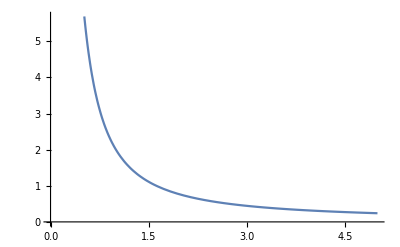

```mathematica
Plot[1/r^2+1/r,{r,0.00000001,5}]
```

```mathematica
Assuming[a>r0[En]&&a>0&&Im[a]==0,Integrate[Sqrt[2m(Veff[r]-En)],{r,a,r1[En]}]]
```

∫_a^((-32 el^2 m+16 el^2 m Z+√(32 En h^2 m+(-32 el^2 m+16 el^2 m Z)^2))/(16 En m)) √2 √(m (-En+h^2/(8 m r^2)+(2 el^2 (-2+Z))/r))ⅆr

```mathematica
r1[1]>r0[1]
```

(-32 e^2 m+16 e^2 m Z+√(32 h^2 m+(-32 e^2 m+16 e^2 m Z)^2))/(16 m)>-(32 e^2 m-16 e^2 m Z+√(32 h^2 m+(-32 e^2 m+16 e^2 m Z)^2))/(16 m)